# CosmoLattice output

## lphi4 model: V(ϕ,X) = 1/4 λ ϕ^4 + 1/2 g^2 ϕ^2 X^2

```mathematica
(* Created by Francisco Torrenti - June 2022 *)
```

```mathematica
(*This notebook reads the output data generated by CosmoLattice (in text format) and creates a series of useful figures. It is adapted to the default lphi4.h model implemented in CosmoLattice, but can be easily generalized to other scalar models. *)
```

```mathematica
Clear["Global`*"] 
(*Clears all variables*)
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
(*Sets working directory to current directory*)
```

## Scale factor

```mathematica
-Graphics-;    (*Column structure of file "average_scale_factor.txt"*)
```

```mathematica
strm=OpenRead["average_scale_factor.txt"];  (*Opens file to read data from*)
(*Skip[strm,String,1];*)  (* If you add headers to the text files, uncomment this to skip the first line *)
NumColumns=4;  (*Number of columns in file*)
scale=ReadList[strm,Table[Number,{NumColumns}]];  (*Reads data and creates table*)
```

```mathematica
FinalTime=scale[[Length[scale]]][[1]];  (*Final time of simulation*)
```

### a(η̃)

```mathematica
sfIn=Interpolation[Table[{scale[[i,1]],scale[[i,2]]},{i,1,Length[scale]}]];   
(*Creates interpolation from columns 1 and 2*)
```

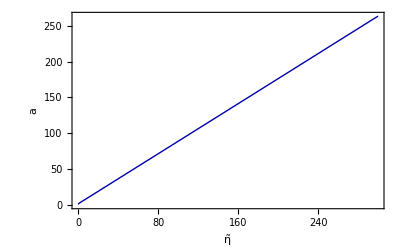

```mathematica
Plot[{sfIn[t]},{t,0,FinalTime},
Frame->True,
FrameLabel->{Style[OverTilde[η],FontSize->16,Black],Style["a",FontSize->16,Black]},
FrameTicksStyle->Directive[Black,14],
PlotStyle->{Darker[Blue],Thick},
ImageSize->400
]
```

### a’(η̃)

```mathematica
sfdIn=Interpolation[Table[{scale[[i,1]],scale[[i,3]]},{i,1,Length[scale]}]];
(*Creates interpolation from columns 1 and 3*)
```

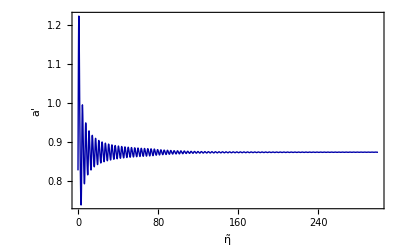

```mathematica
Plot[{sfdIn[t]},{t,0,FinalTime},
Frame->True,PlotRange->All,
FrameLabel->{Style[OverTilde[η],FontSize->16,Black],Style["a'",FontSize->16,Black]},
FrameTicksStyle->Directive[Black,14],
PlotStyle->{Darker[Blue],Thick},
ImageSize->400
]
```

### a’(η̃)/a(η̃)

```mathematica
sfddIn=Interpolation[Table[{scale[[i,1]],scale[[i,4]]},{i,1,Length[scale]}]]; 
(*Creates interpolation from columns 1 and 4*)
```

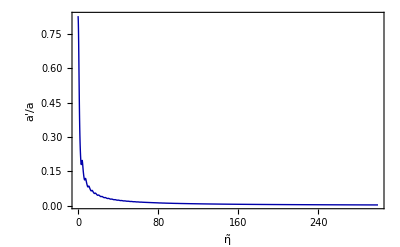

```mathematica
Plot[{sfddIn[t]},{t,0,FinalTime},
Frame->True,PlotRange->All,
FrameLabel->{Style[OverTilde[η],FontSize->16,Black],Style["a'/a",FontSize->16,Black]},
FrameTicksStyle->Directive[Black,14],
PlotStyle->{Darker[Blue],Thick},
ImageSize->400
]
```

## Volume-averages of field 0 (inflaton)

```mathematica
-Graphics-; (*Column structure of file "average_scalar_0.txt"*)
```

```mathematica
strm=OpenRead["average_scalar_0.txt"]; (*Opens file to read data from*)
NumColumns=7;  (*Number of columns in file*)

means0=ReadList[strm,Table[Number,{NumColumns}],RecordLists->True];
(*Reads data and creates table*)
```

```mathematica
(*NOTE: Sometimes "nans" get produced in the last two columns, which the ReadList function cannot read. They must be transformed to "0" in the text file to make it work.*)
```

```mathematica
f0phiIn=Interpolation[Table[{means0[[i,1]][[1]],means0[[i,1]][[2]]},{i,1,Length[means0]}]];
(*Creates interpolation from columns 1 and 2*)
```

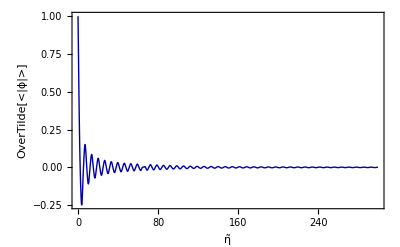

```mathematica
(* Volume average of inflation *)
Plot[f0phiIn[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style[OverTilde["<|ϕ|>"],FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

```mathematica
(* Volume average of inflation --> conformal transformation*)
```

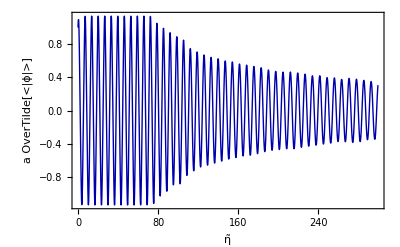

```mathematica
Plot[f0phiIn[t]*sfIn[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style[a OverTilde["<|ϕ|>"],FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

```mathematica
rms0In=Interpolation[Table[{means0[[i,1]][[1]],means0[[i,1]][[6]]},{i,1,Length[means0]}]];
(*Creates interpolation from columns 1 and 6*)
```

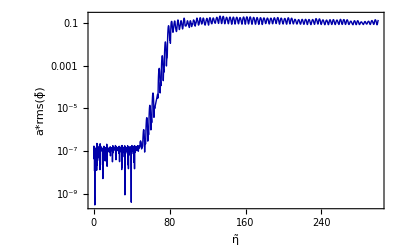

```mathematica
(* rms of inflaton (including conformal transformation) *)
LogPlot[sfIn[t]*rms0In[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style["a*rms(ϕ̃)",FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

## Volume-averages of field 1 (daughter field)

```mathematica
strm=OpenRead["average_scalar_1.txt"]; (*Opens file to read data from*)
NumColumns=7;  (*Number of columns in file*)

means1=ReadList[strm,Table[Number,{NumColumns}],RecordLists->True];
(*Reads data and creates table*)
```

```mathematica
(*NOTE: Sometimes "nans" get produced in the last two columns, which the ReadList function cannot read. They must be transformed to "0" in the text file to make it work.*)
```

```mathematica
f1phiIn=Interpolation[Table[{means1[[i,1]][[1]],means1[[i,1]][[2]]},{i,1,Length[means1]}]];
(*Creates interpolation from columns 1 and 2*)
```

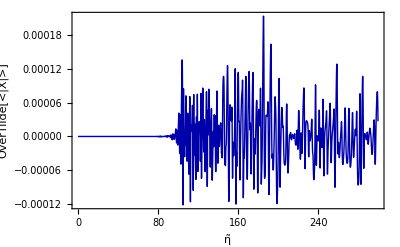

```mathematica
(* Volume average of daughter field *)
Plot[f1phiIn[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style[OverTilde["<|X|>"],FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

```mathematica
(* Volume average of daughter field  --> conformal transformation*)
```

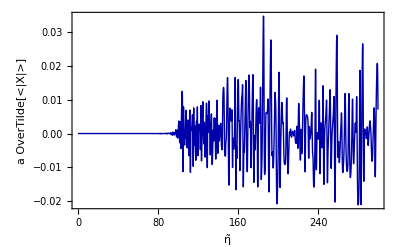

```mathematica
Plot[f1phiIn[t]*sfIn[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style[a OverTilde["<|X|>"],FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

```mathematica
rms1In=Interpolation[Table[{means1[[i,1]][[1]],means1[[i,1]][[6]]},{i,1,Length[means1]}]];
(*Creates interpolation from columns 1 and 6*)
```

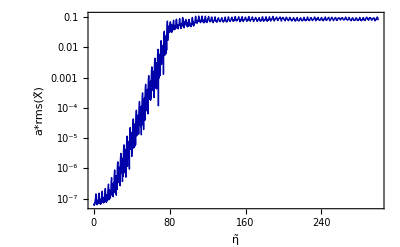

```mathematica
(* rms of daughter field (including conformal transformation) *)
LogPlot[sfIn[t]*rms1In[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style["a*rms(X̃)",FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

## “Energy conservation” (preservation of 1st Friedmann equation)

```mathematica
-Graphics-;
```

```mathematica
strm=OpenRead["average_energy_conservation.txt"];
NumColumns=4;
EnCons=ReadList[strm,Table[Number,{NumColumns}]];
```

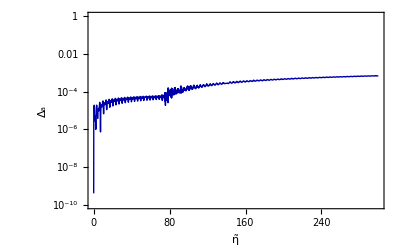

```mathematica
EnConsIn=Interpolation[Table[{EnCons[[i,1]],EnCons[[i,2]]},{i,1,Length[EnCons]}]];
LogPlot[Abs[EnConsIn[t]],{t,0,FinalTime},PlotRange->{10^(-10),1},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,FrameLabel->{Style[η̃,FontSize->16,Black],Style["Δ_a",FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

## Energy density components

```mathematica
-Graphics-;
```

```mathematica
strm=OpenRead["average_energies.txt"];
NumColumns=8;
energy=ReadList[strm,Table[Number,{NumColumns}]];

(* Creates an interpolating function for each energy component*)
Kin0=Interpolation[Table[{energy[[i,1]],energy[[i,2]]},{i,1,Length[energy]}]]; (*Kinetic inflation*)
Grad0=Interpolation[Table[{energy[[i,1]],energy[[i,3]]},{i,1,Length[energy]}]]; (*Gradient inflaton *)
Kin1=Interpolation[Table[{energy[[i,1]],energy[[i,4]]},{i,1,Length[energy]}]]; (*Kinetic daughter field*)
Grad1=Interpolation[Table[{energy[[i,1]],energy[[i,5]]},{i,1,Length[energy]}]]; (*Gradient daughter field*)
Pot=Interpolation[Table[{energy[[i,1]],energy[[i,6]]},{i,1,Length[energy]}]]; (*Inflaton potential *)
Int=Interpolation[Table[{energy[[i,1]],energy[[i,7]]},{i,1,Length[energy]}]]; (*Inflaton-daughter interaction*)
ETot=Interpolation[Table[{energy[[i,1]],energy[[i,8]]},{i,1,Length[energy]}]];  (* Sum of components*)
```

```mathematica
resc=4; (* Coefficient for conformal rescaling *)
```

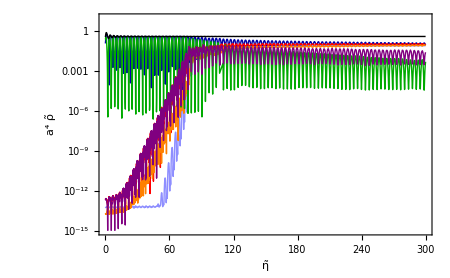

```mathematica
(* Plot of energy components with conformal rescaling *)
LogPlot[{Kin0[t]*sfIn[t]^resc,Grad0[t]*sfIn[t]^resc,Kin1[t]*sfIn[t]^resc,Grad1[t]*sfIn[t]^resc,Pot[t]*sfIn[t]^resc,Int[t]*sfIn[t]^resc,ETot[t]*sfIn[t]^resc},{t,0,FinalTime},

PlotStyle->{{Thick,Darker[Blue]},{Thick,Lighter[Lighter[Blue]]},{Thick,Red},{Thick,Orange},{Thick,Darker[Green]},{Thick,Purple},{Thick,Black}},

ImageSize->450,PlotRange->{10^(-15),10},Frame->True,FrameLabel->{Style[OverTilde[η],FontSize->16,Black],Style["a^4"OverTilde["ρ"],FontSize->16,Black]},FrameTicksStyle->Directive[Black,16]]
```

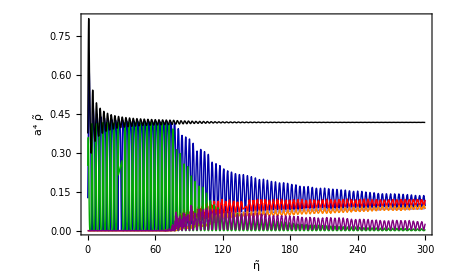

```mathematica
(* Same plot as before but in linear scale*)

Plot[{Kin0[t]*sfIn[t]^resc,Grad0[t]*sfIn[t]^resc,Kin1[t]*sfIn[t]^resc,Grad1[t]*sfIn[t]^resc,Pot[t]*sfIn[t]^resc,Int[t]*sfIn[t]^resc,ETot[t]*sfIn[t]^resc},{t,0,FinalTime},PlotStyle->{{Thick,Darker[Blue]},{Thick,Lighter[Lighter[Blue]]},{Thick,Red},{Thick,Orange},{Thick,Darker[Green]},{Thick,Purple},{Thick,Black}},ImageSize->450,PlotRange->{0,0.82},Frame->True,FrameLabel->{Style[OverTilde[η],FontSize->16,Black],Style["a^4"OverTilde["ρ"],FontSize->16,Black]},FrameTicksStyle->Directive[Black,16]]
```

## Parameters for spectra outputs

```mathematica
(* Parameters from the simulation *)
  Npoints=32;   (* N: number of lattice points per side *)
  tOutputInfreq=1;  (* time interval between spectra *)
  NumBins=IntegerPart[Sqrt[3]* Npoints/2]; (* number of bins in the spectra *)

(* Parameters for spectra output *)
  s3=1 ; (* frequency of spectra output. Spectra printed are s3*n+1 for n=1, 2,... *)
```

```mathematica
(*Number of spectra to be printed*)
NumSpectra=FinalTime/(tOutputInfreq*s3)
```

299.9

```mathematica
colors=Table[ColorData["Rainbow", t],{t,1,0,-1/NumSpectra}]; (*creates a rainbow of colours for spectra figures*)
```

```mathematica
specTimes=Table[tOutputInfreq*s3*(i-1),{i,1,NumSpectra*s3}]; (*approximate spectra times*)
```

## Spectra Fields

```mathematica
-Graphics-;
```

### Inflaton

```mathematica
NumColumns=5;
specS0=ReadList["spectra_scalar_0.txt",Table[Number,{NumColumns}]];
```

```mathematica
Table[
spectraS0[i]=Table[{specS0[[j]][[1]],specS0[[j]][[2]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
Table[
spectraS0d[i]=Table[{specS0[[j]][[1]],specS0[[j]][[3]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
Table[
partnumb0[i]=Table[{specS0[[j]][[1]],specS0[[j]][[4]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
```

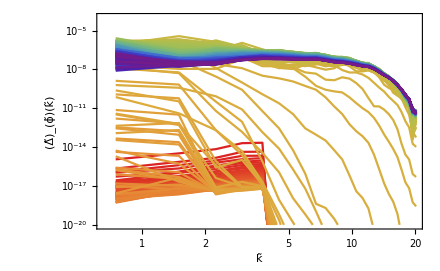

```mathematica
(*Spectrum of inflaton amplitude*)
ListLogLogPlot[Table[spectraS0[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{(10^(-20)),10^(-4)},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["(Δ̃)_(ϕ̃)(k̃)",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14]]
```

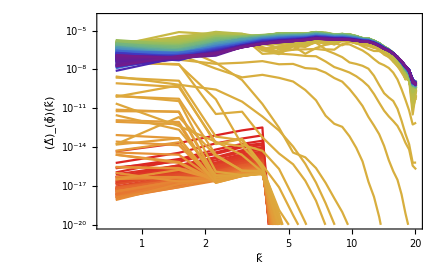

```mathematica
(*Spectrum of inflaton time-derivative*)
ListLogLogPlot[Table[spectraS0d[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{(10^(-20)),10^(-4)},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["(Δ̃)_(OverscriptBox[ϕ, ~]')(k̃)",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14]]
```

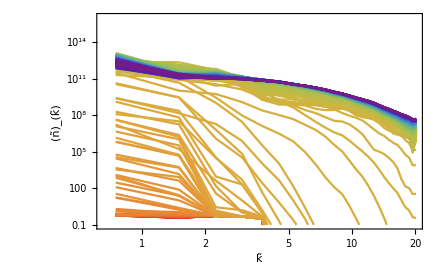

```mathematica
(*Particle number of inflaton*)
ListLogLogPlot[Table[partnumb0[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{(10^(-1)),10^16},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["(ñ)_(k̃)",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14]]
```

### Daughter field

```mathematica
NumColumns=5;
specS1=ReadList["spectra_scalar_1.txt",Table[Number,{NumColumns}]];
```

```mathematica
Table[
spectraS1[i]=Table[{specS1[[j]][[1]],specS1[[j]][[2]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
Table[
spectraS1d[i]=Table[{specS1[[j]][[1]],specS1[[j]][[3]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
Table[
partnumb1[i]=Table[{specS1[[j]][[1]],specS1[[j]][[4]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
```

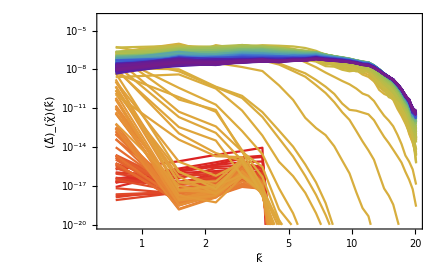

```mathematica
(*Spectrum of daughter field amplitude*)
ListLogLogPlot[Table[spectraS1[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{(10^(-20)),10^(-4)},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["(Δ̃)_(χ̃)(k̃)",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14]]
```

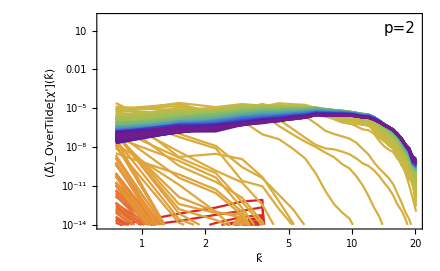

```mathematica
(*Spectrum of daughter field time-derivative*)
ListLogLogPlot[Table[spectraS1d[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{(10^(-14)),10^2},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["(Δ̃)_OverTilde[χ'](k̃)",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14],
Epilog->{Text[Style["p=2",15,FontFamily->"CMUSerif-Italic"],Scaled[{0.93,0.93}]]}]
```

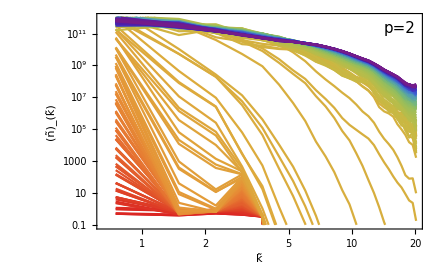

```mathematica
(*Particle number of daughter field*)
ListLogLogPlot[Table[partnumb1[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{0.1,10^12},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["(ñ)_(k̃)",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14],
Epilog->{Text[Style["p=2",15,FontFamily->"CMUSerif-Italic"],Scaled[{0.93,0.93}]]}]
```